## Simple Wordle Solver

## Core Functions

```mathematica
(*Function to generate regexs to do basic filter (2s only)*)
FilterTwos[wordList_,assocs_]:=Module[{keys=Keys[assocs],regexs,temp},
(*Create a regex for each attempt*)
regexs=Table[(*For each key*)
StringRiffle[MapThread[If[#2==2,#1,"."]&,{StringPartition[key,1],attempts⟦key⟧}],""]
,{key,Keys[attempts]}];
(*Apply each regex to word list*)
temp=Table[Pick[wordList,StringMatchQ[#,RegularExpression[reg]]&/@wordList],{reg,regexs}];
(*Take intersection of the resulting lists*)
Intersection@@temp
] 
(*Filter out all impossible words based on lack of required letter (1 in attempt)*)
FilterOnes[wordList_,assocs_]:=Module[{keys=Keys[assocs],containsAll,wrongWords,temp,regexs},
(*Find the words which contain the letters from each attempt*)
containsAll=Intersection@@Table[(*For each key*)
(*Grab the letters which are in the word ie 1s and 2s*)
temp=Pick[StringPartition[key, 1],Map[#>0&,assocs⟦key⟧]];
(*Find and filter all words from wordList which contain all of these letters*)
Pick[wordList,Table[AllTrue[StringContainsQ[word,#]&/@temp,TrueQ],{word,wordList}]]
,{key,keys}];
(*Find list of words with letters not in the wrong spots*)
regexs=Table[(*For each key*)
Table[
StringRiffle[MapThread[If[#2==1,#1,"."]&,{StringPartition[key,1],val}],""]
,{val,Select[DiagonalMatrix[Map[If[#==1,1,0]&,attempts⟦key⟧]],Norm[#]≠0&]}],
{key,Keys[attempts]}]//Flatten;
wrongWords=Union@@Table[Pick[wordList,StringMatchQ[#,RegularExpression[reg]]&/@wordList],{reg,regexs}];
(*Find the complement of the set of all words containing the proper letters and all words with the letters in the wrong spot*)
Complement[containsAll,wrongWords]
] 
(*Filter out all impossible words based on the presence of a incorrect letter (0 in attempt)*)
FilterZeros[wordList_,assocs_]:=Module[{temp,wrongWords},
(*All words which cannot appear because they contain a letter not allowed*)
wrongWords=Union@@Table[(*For each attempt*)
(*Grab the letters which are not in the word ie 0s*)temp=Pick[StringPartition[key, 1],Map[#==0&,attempts⟦key⟧]];
(*Find and filter all words from wordList which contain any of these letters*)
Pick[wordleWords,Table[AnyTrue[StringContainsQ[word,#]&/@temp,TrueQ],{word,wordleWords}]]
,{key,Keys[attempts]}];
(*Remove all wrong words from list of possible words*)
Complement[wordleWords,wrongWords]
]
```

```mathematica
WordleNextGuess[dictionary_,attempts_]:=Module[{words,freqs},
words=Intersection[FilterTwos[dictionary,attempts],FilterOnes[dictionary,attempts],FilterZeros[dictionary,attempts]];
Print[words];
freqs=WordFrequencyData[#,"Total"]&/@words;
(*Display word frequency information*)
BarChart[freqs/(Total[freqs]),
ChartLabels->words,
BarOrigin->Left,ImageSize->Full, PlotTheme->"Detailed"]
]
```

## Startup

#### Get the list of all words, and extract only those which are 5 letters long

```mathematica
wordleWords=Select[WordList["KnownWords"],StringLength[#]==5&];wordleStartWords=Select[WordList["CommonWords"],StringLength[#]==5&];
```

#### Distribution of letters

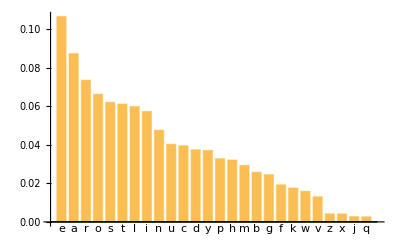

```mathematica
letterCounts=LetterCounts[StringJoin[wordleStartWords],IgnoreCase->True];
ℒ𝒟=CategoricalDistribution[Keys[letterCounts],Values[letterCounts]];
Information[ℒ𝒟,"ProbabilityPlot"]
```

#### Get initial word

```mathematica
initialGuess=Module[{startWords,wordLetterList,wordList,listInd},
startWords={};
While[startWords=={},
(*Random sample 5 letters without replacement using frequencey weighting from above*)
wordLetterList=RandomSample[Values[letterCounts]->Keys[letterCounts],5];
(*List of all orderings of the letters*)
wordList=StringRiffle[#,""]&/@Permutations[wordLetterList];
(*Check if any of the permuations are actually "words"*)
listInd=AnyTrue[Table[#===i,{i,wordleStartWords}],TrueQ]&/@wordList;
startWords=Pick[wordList,listInd];
];
Print[wordLetterList];
Print[startWords];
(*If multiple permuations are words ties are broken with word frequency*)
startWords⟦Ordering[WordFrequencyData/@startWords,-1]⟧⟦1⟧
]
```

{m,p,s,c,a}

{scamp}

scamp

## Example

```mathematica
attempts=<|"plumb"->{0,0,0,0,1},
"stray"->{0,1,1,0,0}|>
```

<|plumb→{0,0,0,0,1},stray→{0,1,1,0,0}|>

{biter,brent,britt,broth,Ibert,orbit,robot,tribe}

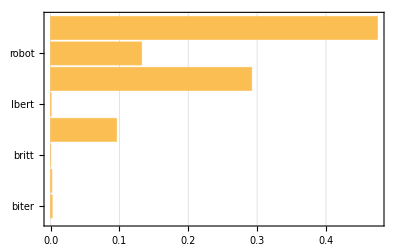

```mathematica
WordleNextGuess[wordleWords,attempts]
```

```mathematica
attempts=<|"reals"->{0,0,0,0,0},"pinto"->{2,1,1,1,1}|>
```

<|reals→{0,0,0,0,0},pinto→{2,1,1,1,1}|>

{point}

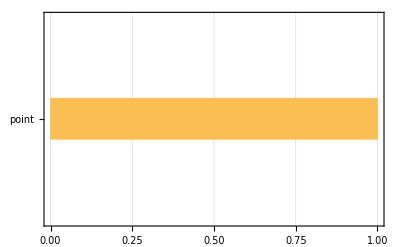

```mathematica
WordleNextGuess[wordleWords,attempts]
```